### Prepare

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/opentf/exoplanets/benfold

## Benfold’s Law

### Introduction to Benfold’s Law

Wikipedia:https://en.wikipedia.org/wiki/Benford’s_law

The distribution of first digits, according to Benford’s law. Each bar represents a digit, and the height of the bar is the percentage of numbers that start with that digit. (From that wikipedia page)

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/thumb/4/46/Rozklad_benforda.svg/512px-Rozklad_benforda.svg.png"]
```

-Graphics-

Here is the theoretical histogram of Benfold’s law.

```mathematica
benList=Table[N@Log10[1+1/d],{d,1,9}];
```

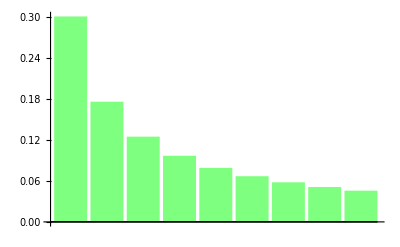

```mathematica
barBen=BarChart[Style[benList,Green],ChartBaseStyle->Opacity[0.5],ChartStyle->EdgeForm[None]]
```

### Benfold’s Law of Exoplents

Here we are going to test Benfold’s Law on Exoplanets.

```mathematica
name = AstronomicalData["Exoplanet"];
```

#### Mass Data

```mathematica
massRaw = AstronomicalData["Exoplanet","Mass"];
mass = Delete[massRaw,Position[massRaw,Missing["NotAvailable"]]];
lenM=Length@mass
```

545

```mathematica
sortM=Sort@Table[RealDigits[mass][[i,1,1]],{i,1,lenM}];
```

```mathematica
tallyM=Tally@sortM;
barListM=Table[N[tallyM[[i,2]]/lenM],{i,1,Length@tallyM}]
```

{0.311927,0.166972,0.150459,0.110092,0.0715596,0.0642202,0.0477064,0.0330275,0.0440367}

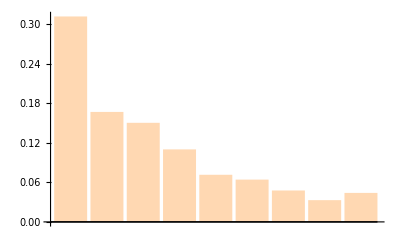

```mathematica
barM=BarChart[Style[barListM,Orange],ChartBaseStyle->Opacity[0.3],ChartStyle->EdgeForm[None]]
```

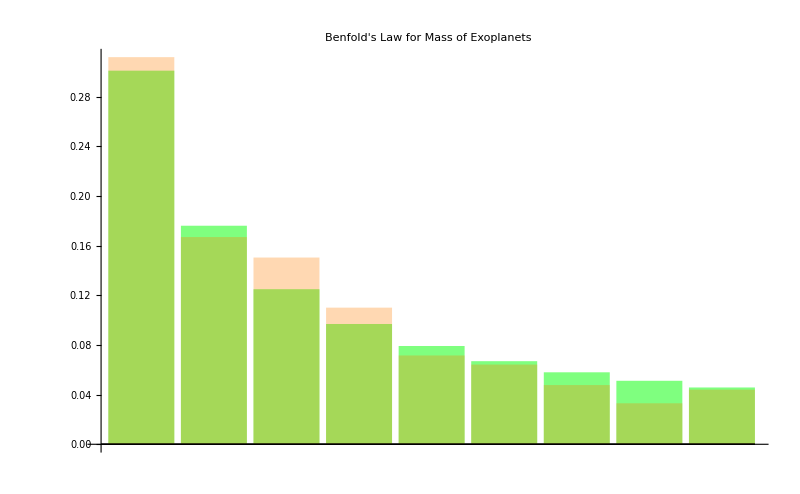

```mathematica
barMvB=Show[barBen,barM,ImageSize->800,PlotLabel->"Benfold's Law for Mass of Exoplanets"]
```

```mathematica
Export["export/barMvB.png",barMvB]
```

export/barMvB.png

```mathematica
deviPerM=Table[NumberForm[(benList[[i]]-barListM[[i]])*100,3],{i,1,9}]
Grid[{Prepend[Table[i,{i,1,9}],"Number"],Prepend[deviPerM,"Deviation(%)"]},Frame->All]
```

{-1.09,0.912,-2.55,-1.32,0.762,0.273,1.03,1.81,0.172}

Number | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
Deviation(%) | -1.09 | 0.912 | -2.55 | -1.32 | 0.762 | 0.273 | 1.03 | 1.81 | 0.172

#### Radius Data

```mathematica
radiusRaw=AstronomicalData["Exoplanet","Radius"];
radius = Delete[radiusRaw,Position[radiusRaw,Missing["NotAvailable"]]];
lenR=Length@radius
```

157

```mathematica
sortR=Sort@Table[RealDigits[radius][[i,1,1]],{i,1,lenR}];
```

```mathematica
tallyR=Tally@sortR
barListR=Table[N[tallyR[[i,2]]/lenR],{i,1,Length@tallyR}]
```

{{1,35},{2,6},{3,4},{4,6},{5,6},{6,13},{7,26},{8,34},{9,27}}

{0.22293,0.0382166,0.0254777,0.0382166,0.0382166,0.0828025,0.165605,0.216561,0.171975}

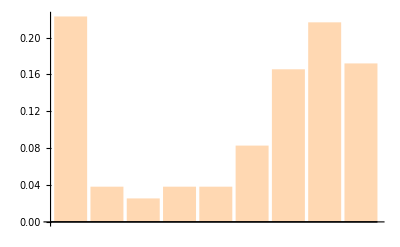

```mathematica
barR=BarChart[Style[barListR,Orange],ChartBaseStyle->Opacity[0.3],ChartStyle->EdgeForm[None]]
```

No Benfold’s Law!